```mathematica
SetDirectory[NotebookDirectory[]];
```

```mathematica
(*ArcTan[(x-5)^2]*)
```

## Benchmark

```mathematica
Needs["NumericalDifferentialEquationAnalysis`"];
```

#### Comparison with GaussNumber

```mathematica
Gauss[n_,a_,b_]:=Module[{aux,Wivec,fvec, valor},
(*"n" representa o número de pontos de integração*)
aux=SetPrecision[GaussianQuadratureWeights[n,a,b],MachinePrecision];
Wivec=aux[[All,2]];
fvec=aux[[All,1]];
For[i=1,i≤ Length[fvec],i++,
fvec[[i]]=f[fvec[[i]]];
];
valor=fvec.Wivec;
Return[valor];
];
```

```mathematica
GaussNumber[a_,b_]:=Module[{n,Optimal,ref}, 
n=1;
ref=NIntegrate[f[x],{x,a,b}];
While[Abs[Gauss[n,a,b]-Gauss[n+1,a,b]]>10^-10,If[n<9,Optimal=n,Break[]];n++];
Optimal=n;
Return [Optimal];(*Return the number of integration points*)
]
```

#### Initial Data

```mathematica
a=-10; (*Menor limite de integração*)
b=10;(*Maior limite de integração*)
e=1.0; (*espaçamento*)
c5=Table[a+i*e  -e ->  a+i*e ,{i,1,(b-a)*(1/e)}];
ϵd=10^-5; 
(*apox da derivada*)
maxavailable=10;
```

```mathematica
f[x_]=ArcTan[(x-5)^2];Sin[x];
```

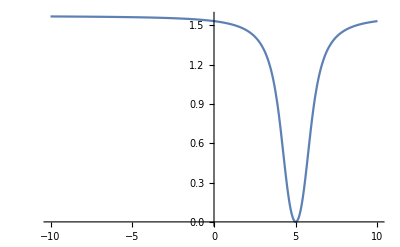

```mathematica
Plot[f[x],{x,a,b},PlotRange->All]
```

## Method considering derivates, changing for high order derivatives approximations (https://en.wikipedia.org/wiki/Finite_difference_coefficient)

#### Numerical Derivative:

```mathematica
(*First derivate approximation*)
```

```mathematica
dfdx1[x_]:=Module[{derivate,h=ϵd},
derivate=(-f[x+2h]+8f[x+h]-8f[x-h]+f[x-2h])/(12h);
Return[derivate];
]
```

```mathematica
(*Second derivate approximation*)
```

```mathematica
dfdx2[x_]:=Module[{derivate,h=ϵd*10^1},
derivate=(-f[x+2h]+16f[x+h]-30f[x]+16f[x-h]-f[x-2h])/(12 h^2);
Return[derivate];
]
```

```mathematica
(*Third derivate approximation*)
```

```mathematica
dfdx3[x_]:=Module[{derivate,h=ϵd*10^2},
derivate=(f[x+2h]-2f[x+h]+2f[x-h]-f[x-2h])/(2 h^3);
Return[derivate];
]
```

```mathematica
(*Fourfth derivate approximation*)
```

```mathematica
dfdx4[x_]:=Module[{derivate,h=ϵd*10^3},
derivate=(f[x+2h]-4f[x+h]+6f[x]-4f[x-h]+f[x-2h])/(h^4);
Return[derivate];
]
```

```mathematica
(*Fifth derivate approximation*)
```

```mathematica
dfdx5[x_]:=Module[{derivate,h=ϵd*10^4},
derivate=(-f[x-3h]+4f[x-2h]-5f[x-h]+5f[x+h]-4f[x+2h]+f[x+3h])/(2 h^5);
Return[derivate];
]
```

```mathematica
Partial[x_]:=Module[{β,fx},
β=ϵd;
fx=Catch[If[Abs[dfdx1[x]]< β,Throw[1],
	If[Abs[dfdx2[x]]< β,Throw[1],
	If[Abs[dfdx3[x]]< β,Throw[2],
	If[Abs[dfdx4[x]]< β,Throw[2],
	If[Abs[dfdx5[x]]< β,Throw[3],Throw[maxavailable]]]]]]];
Return[fx];
];
```

#### Derivative Analysis:

```mathematica
(*Not using derivates approximations*)
```

```mathematica
DerivateAnalisysd1[a1_,b1_]:=Module[{a,b,min, max,aux,ref0,ref,diferenced1},
a=Min[a1,b1];
b=Max[a1,b1];
(*Retorna a diferença entre o maior e o menor valor absoluto da primeira derivada da função f[x] para o intervalo (a,b)*)
min=max=Abs[dfdx1[a]];
aux=5;
For[i=0,i≤aux,i++;ref=Abs[dfdx1[a+i*(b-a)/aux]];
If[ref<min ,min=ref];
If[ref>max,max=ref];
];
(*Finds the min and max value for second derivate*)
diferenced1=max-min;
Return[diferenced1//N];
]
```

```mathematica
DerivateAnalisysd2[a1_,b1_]:=Module[{a,b,min, max,aux,ref,diferenced2},
a=Min[a1,b1];
b=Max[a1,b1];
(*Retorna a diferença entre o maior e o menor valor absoluto da segunda derivada da função f[x] para o intervalo (a,b)*)
min=max=Abs[dfdx2[a]];
aux=5;
For[i=0,i≤aux,i++;ref=Abs[dfdx2[a+i*(b-a)/aux]];
If[ref<min ,min=ref];
If[ref>max,max=ref];
];
(*Finds the min and max value for second derivate*)
diferenced2=max-min;
Return[diferenced2//N];
]
```

#### Gauss Number 2

```mathematica
GaussNumberII[x0_,x1_]:=Module[{n,Optimal, α=Abs[b-a],maxintorder,minintorder,result,test}, 
ϵ=Exp[-α/Abs[x0-x1]]; (*quanto menor o intervalo, menor sera o valor de ϵ (mais perto de zero), e quanto menor ϵ, menos pontos de integração serão necessários*)
maxintorder=Max[Partial[x0],Partial[x1]];
minintorder=Min[Partial[x0],Partial[x1]];
minintorder=If[minintorder<maxavailable,minintorder,3(*caso os dois pontos retornem dfdx5>β*)];
dfdx=DerivateAnalisysd1[x0,x1]; 
df2dx2=DerivateAnalisysd2[x0,x1];
n=IntegerPart[Exp[(df2dx2)/(dfdx+10^-15)]];
Optimal=IntegerPart[n];
result=If[Optimal<minintorder,minintorder,If[Optimal>maxintorder,maxintorder,Optimal]];
Return[result];
];
```

## Gauss Number 3 (Integration points number)

```mathematica
GaussNumberIII[x0_,x1_]:=Module[{np=3,n,Optimal,maxintorder,minintorder,avgdfdx1,avgdfdx2}, 
intpoinsdistribution=Table[Partial[Range[x0,x1,(x1-x0)/np][[i]]],{i,1,np+1}];
maxintorder=Max[intpoinsdistribution];
minintorder=Min[intpoinsdistribution];
avgdfdx1=Mean[Table[Abs[dfdx1[Range[x0,x1,(x1-x0)/np][[i]]]],{i,1,np+1}]]//N;
avgdfdx2=Mean[Table[Abs[dfdx2[Range[x0,x1,(x1-x0)/np][[i]]]],{i,1,np+1}]]//N;
n=IntegerPart[Exp[(avgdfdx2)/(avgdfdx1+10^-15)]]+2;
Optimal=If[minintorder<n && n<=maxintorder,n,If[n>maxintorder,maxintorder,minintorder]];
Optimal=If[minintorder==maxintorder,If[n>maxintorder,maxintorder,n],Optimal];
(*Print[intpoinsdistribution];
Print[{avgdfdx1,avgdfdx2,Abs[avgdfdx2/(avgdfdx1+avgdfdx2)],Log[Abs[avgdfdx2/(avgdfdx1+avgdfdx2)]],Log[Abs[1/avgdfdx2]]}];
Print[{maxintorder,minintorder,n}];*)
Return[Optimal];
];
```

```mathematica
GaussNumberIII[-8,-7]
```

3

```mathematica
ComparisonIntegrate[x0_,x1_]:=Module[{gn1,nint},
gn1=Gauss[GaussNumberIII[x0,x1],x0,x1];
nint=NIntegrate[f[x],{x,x0,x1}];
Return[Abs[gn1-nint]]//N;
]
```

```mathematica
dataNpoints=Table[GaussNumberIII[(a+i*e)-e,a+i*e],{i,1,(b-a)*(1/e)}];
dataError=Table[ComparisonIntegrate[(a+i*e)-e,a+i*e],{i,1,(b-a)*(1/e)}];
```

```mathematica
TableForm[Table[GaussNumber[(a+i*e)-e,a+i*e],{i,1,(b-a)*(1/e)}],TableHeadings-> {c5,{"Gauss"}}]&&
TableForm[dataNpoints,TableHeadings-> {{},{"metodo novo"}}]&&
TableForm[dataError,TableHeadings-> {{},{"d2"}}]
(*Variação por espaço do subintervalo!*)
```

-10.→-9. | 3
-9.→-8. | 3
-8.→-7. | 3
-7.→-6. | 3
-6.→-5. | 3
-5.→-4. | 3
-4.→-3. | 3
-3.→-2. | 4
-2.→-1. | 4
-1.→0. | 4
0.→1. | 4
1.→2. | 5
2.→3. | 6
3.→4. | 8
4.→5. | 9
5.→6. | 9
6.→7. | 8
7.→8. | 6
8.→9. | 5
9.→10. | 4&& | 3
 | 3
 | 3
 | 3
 | 3
 | 3
 | 3
 | 3
 | 3
 | 3
 | 3
 | 4
 | 5
 | 5
 | 9
 | 9
 | 5
 | 5
 | 4
 | 3&& | 1.28009×10^-12
 | 2.2693×10^-12
 | 4.20286×10^-12
 | 8.19433×10^-12
 | 1.69729×10^-11
 | 3.78089×10^-11
 | 9.20537×10^-11
 | 2.50404×10^-10
 | 7.84965×10^-10
 | 2.96647×10^-9
 | 1.44465×10^-8
 | 5.41061×10^-10
 | 1.50674×10^-10
 | 7.94244×10^-8
 | 6.08333×10^-11
 | 6.08333×10^-11
 | 7.94244×10^-8
 | 1.50674×10^-10
 | 5.41061×10^-10
 | 1.44465×10^-8

## Rendering plots

```mathematica
fontsize=20;
res=400;
```

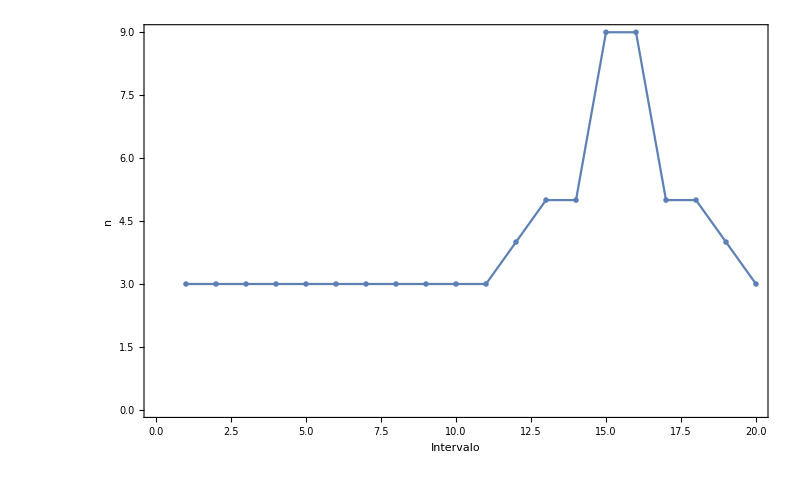

```mathematica
ErrorPlot =ListPlot[dataError/1000,PlotMarkers->{Automatic, Large},Joined->True,Frame->True,FrameStyle->Directive[Black,Bold, FontSize->fontsize],FrameLabel->{ Style[" Intervalo ",FontSize->fontsize],"Abs[error] "},ImageSize->800];
MinimumPlot =ListPlot[dataNpoints,PlotMarkers->{Automatic, Large},Joined->True,Frame->True,FrameStyle->Directive[Black,Bold, FontSize->fontsize],FrameLabel->{ Style[" Intervalo ",FontSize->fontsize]," n "},ImageSize->800]
```

## Comparison plot

```mathematica
Refminimumdata={3,3,3,3,3,3,3,4,4,4,4,5,6,8,9,9,8,6,5,4};
```

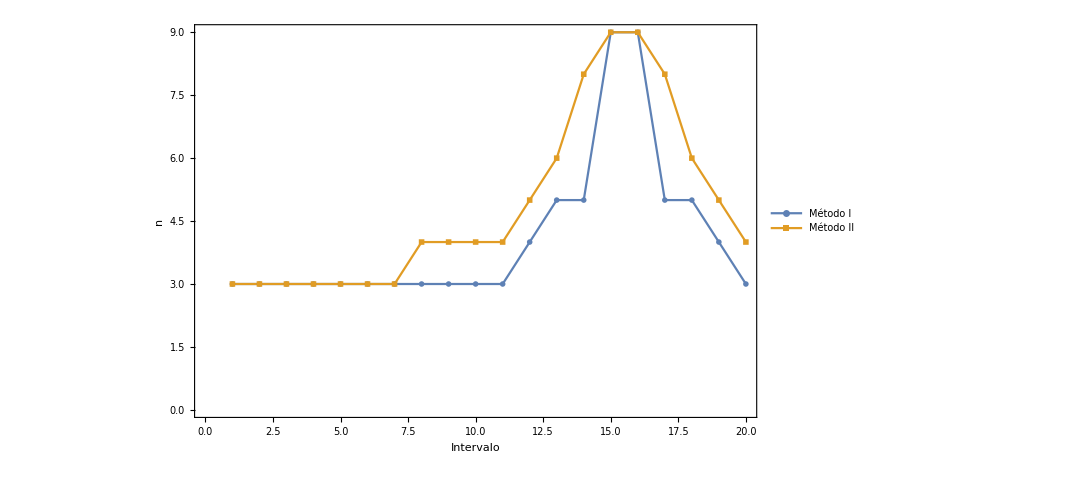

```mathematica
ComparisonPlot=ListPlot[{dataNpoints,Refminimumdata},PlotMarkers->{Automatic, Large},PlotLegends->{Style["Método I",FontSize->fontsize],Style[ "Método II",FontSize->fontsize]},Joined->True,Frame->True,FrameStyle->Directive[Black,Bold, FontSize->fontsize],FrameLabel->{ Style[" Intervalo ",FontSize->fontsize]," n "},ImageSize->800]
```

## Exporting data

```mathematica
ExportPlotsQ=True;
If[ExportPlotsQ,
Export["NpointsMethodII.png",MinimumPlot,ImageResolution->res];
Export["NpointsComparison.png",ComparisonPlot,ImageResolution->res];
Export["ErrorplotmethodII.png",ErrorPlot,ImageResolution->res];
];
```